```mathematica
SetDirectory[NotebookDirectory[]];
(files=FileNames["data/*"])//TableForm
```

data\bla1.csv
data\einzel.csv
data\erstemessung.ods
data\frequenzdoppel.ods
data\hauen1.csv
data\placeholder.txt
data\pockel.ods
data\tem00b.txt
data\tem00.txt
data\tem03.2.bmp
data\tem032b.txt
data\tem032.txt
data\tem03.bmp
data\tem10.bmp
data\tem10b.txt
data\tem10.txt
data\tem20.bmp
data\tem20b.txt
data\tem20.txt
data\zweitemesseung.ods

```mathematica
str=OpenRead[files⟦1⟧];
ReadList[str,String,2];
bla=ReadList[str,{Number,Number,Number}];
str=OpenRead[files⟦2⟧];
ReadList[str,String,2];
einzel=ReadList[str,{Number,Number,Number}];
str=OpenRead[files⟦5⟧];
ReadList[str,String,2]
hauen=ReadList[str,{Number,Number}];
```

{Zeit Kanal A,(ms) (mV)}

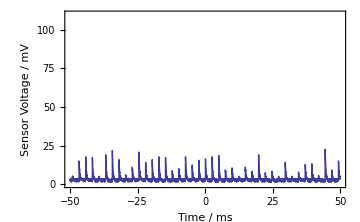
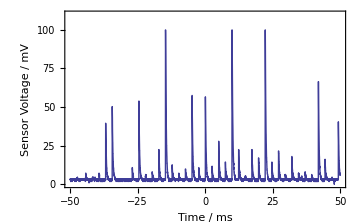

```mathematica
ListPlot[{{#⟦1⟧,#⟦2⟧}&/@#},PlotRange->{All,{0,110}},Joined->True,Frame->True,Axes->None,FrameLabel->{"Time / ms","Sensor Voltage / mV"},ImageSize->Medium]&/@{bla,hauen}
```

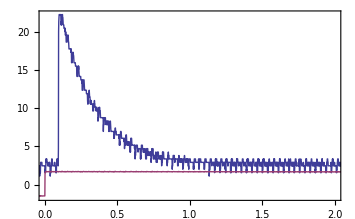

```mathematica
ListPlot[{{#⟦1⟧,#⟦2⟧}&/@einzel,{#⟦1⟧,#⟦3⟧}&/@einzel},PlotRange->{{0,2},All},Joined->True,Frame->True,Axes->None]
```

```mathematica
ListPlot[{{#⟦1⟧,#⟦2⟧}&/@einzel,{#⟦1⟧,#⟦3⟧}&/@einzel},PlotRange->{{0,2},All},Joined->True,Frame->True,Axes->None]
```